## Core parameters

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Dynamic γ

```mathematica
G=0.1;ginit=0.4;
sampleinits={{0.7,0.1},{0.1,0.7},{0.2,0.1}};
```

```mathematica
dy1[y1_,y2_,γ_]:=y1((p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_,γ_]:=y2 ((p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
```

```mathematica
sol[{y1init_,y2init_},Gon_]:=NDSolve[{y1'[t]==dy1[y1[t],y2[t],g[t]],y2'[t]==dy2[y1[t],y2[t],g[t]],(*g evolves according to dg*)g'[t]==If[Gon==True&&g[t]>0&&g[t]<1,If[Sign[dy1[y1[t],y2[t],g[t]]]==0,0, -1  Sign[dy1[y1[t],y2[t],g[t]]] G ],0],(*initial conditions*)y1[0]==y1init,y2[0]==y2init,g[0]==ginit},{y1,y2,g},{t,0,100}];
```

```mathematica
inits={};
Table[If[i+j<1,AppendTo[inits,{i,j}]],{i,0.1,1,0.1},{j,0.1,1,0.1}];
```

```mathematica
trajectoriesoff=Table[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]],False]⟦1⟧],{t,0,100,0.05}],{j,1,Length[inits],1}];
trajectorieson=Table[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]],True]⟦1⟧],{t,0,100,0.05}],{j,1,Length[inits],1}];
```

General::munfl: 9.82822×10^-297 1.06581×10^-14 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.42781×10^-298 1.06581×10^-14 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.96321×10^-304 1.06581×10^-14 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
tolerance=0.01;
fixcolours[traj_]:=Table[
If[
AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{1,0,0}]<tolerance],TrueQ],cols⟦1⟧,
If[AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{0,1,0}]<tolerance],TrueQ],cols⟦3⟧,
If[AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{0,0,1}]<tolerance],TrueQ],cols⟦2⟧,Gray]]]
,{i,1,Length[traj],1}];
```

```mathematica
coloursoff=fixcolours[trajectoriesoff];
colourson=fixcolours[trajectorieson];
```

```mathematica
(*(*Plot y1 and y2 together*)Table[Plot[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]]]],{t,0,100},PlotStyle->Automatic],{j,1,Length[inits],1}]//Show
*)
ternploff=TernaryListPlot[trajectoriesoff,Joined->True,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotStyle->coloursoff];
ternplon=TernaryListPlot[trajectorieson,Joined->True,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotStyle->colourson];
```

```mathematica
initstopl=Table[{{sampleinits⟦i,1⟧,1-sampleinits⟦i,1⟧-sampleinits⟦i,2⟧,sampleinits⟦i,2⟧}},{i,1,Length[sampleinits]}]
```

{{{0.7,0.2,0.1}},{{0.1,0.2,0.7}},{{0.2,0.7,0.1}}}

```mathematica
initsplotted=TernaryListPlot[initstopl,Joined->False,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotMarkers->Automatic,PlotStyle->Black]
```

-Graphics-

```mathematica
goff=Show[ternploff,initsplotted,
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]];
```

```mathematica
gon=Show[ternplon,initsplotted,
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]];
```

```mathematica
GraphicsRow[{goff,gon}]
```

-Graphics-

```mathematica
gon
```

-Graphics-

```mathematica
Table[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t],Sign[dy1[y1[t],y2[t],g[t]]]}/.sol[{0.33,0.33},True]],{t,0,100}]
```

General::munfl: 8.13249×10^-299 1.59872×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.82129×10^-126 1.92916×10^-251 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.60675×10^-148 5.16332×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{0.33,0.33,0.34,0.4,-1}},{{0.243723,0.306158,0.450119,0.5,-1}},{{0.128279,0.199517,0.672204,0.6,-1}},{{0.0322962,0.0569417,0.910762,0.7,-1}},{{0.00491407,0.00934909,0.985737,0.8,-1}},{{0.000585563,0.00116535,0.998249,0.9,-1}},{{0.0000580221,0.000117217,0.999825,1.,-1}},{{5.2625×10^-6,0.0000106314,0.999984,1.,-1}},{{4.77903×10^-7,9.65467×10^-7,0.999999,1.,-1}},{{4.38125×10^-8,8.85107×10^-8,1.,1.,-1}},{{3.81514×10^-9,7.7074×10^-9,1.,1.,-1}},{{3.84397×10^-10,7.76565×10^-10,1.,1.,-1}},{{1.02514×10^-31,1.89424×10^-22,1.,0.969031,-1}},{{-4.93038×10^-63,-7.60502×10^-35,1.,0.977849,1}},{{-1.11704×10^-87,-1.22295×10^-46,1.,0.994151,1}},{{1.1132×10^-101,2.09578×10^-50,1.,1.,-1}},{{4.91065×10^-126,7.98802×10^-63,1.,1.,-1}},{{8.03377×10^-149,1.05352×10^-74,1.,1.,-1}},{{4.69194×10^-173,2.61674×10^-86,1.,0.986135,-1}},{{1.64259×10^-197,2.91608×10^-98,1.,0.969832,-1}},{{-2.63301×10^-211,-4.8243×10^-110,1.,0.975665,1}},{{-1.71799×10^-235,1.2935×10^-121,1.,0.991967,1}},{{1.78728×10^-249,-1.56793×10^-125,1.,1.,-1}},{{2.26656×10^-273,-3.2131×10^-139,1.,1.,-1}},{{9.3551×10^-298,2.9035×10^-151,1.,1.,-1}},{{0.,5.86828×10^-165,1.,0.940875,0}},{{0.,-7.97986×10^-164,1.,0.840875,0}},{{0.,-2.12537×10^-163,1.,0.740875,0}},{{0.,-3.71487×10^-163,1.,0.640875,0}},{{0.,-5.3579×10^-163,1.,0.540875,0}},{{0.,-6.84587×10^-163,1.,0.440875,0}},{{0.,-7.97019×10^-163,1.,0.340875,0}},{{0.,-8.52226×10^-163,1.,0.240875,0}},{{0.,-8.29349×10^-163,1.,0.140875,0}},{{0.,-7.07529×10^-163,1.,0.040875,0}},{{0.,-4.9576×10^-163,1.,0.,0}},{{0.,-3.04558×10^-163,1.,0.,0}},{{0.,-1.43456×10^-163,1.,0.,0}},{{0.,-8.88354×10^-165,1.,0.,0}},{{0.,1.0273×10^-163,1.,0.,0}},{{0.,1.94956×10^-163,1.,0.,0}},{{0.,2.71366×10^-163,1.,0.,0}},{{0.,3.3553×10^-163,1.,0.,0}},{{0.,3.91018×10^-163,1.,0.,0}},{{0.,4.41403×10^-163,1.,0.,0}},{{0.,4.87428×10^-163,1.,0.,0}},{{0.,5.18961×10^-163,1.,0.,0}},{{0.,5.36161×10^-163,1.,0.,0}},{{0.,5.40727×10^-163,1.,0.,0}},{{0.,5.34361×10^-163,1.,0.,0}},{{0.,5.18762×10^-163,1.,0.,0}},{{0.,4.95632×10^-163,1.,0.,0}},{{0.,4.66671×10^-163,1.,0.,0}},{{0.,4.33578×10^-163,1.,0.,0}},{{0.,3.98055×10^-163,1.,0.,0}},{{0.,3.61951×10^-163,1.,0.,0}},{{0.,3.26889×10^-163,1.,0.,0}},{{0.,2.92886×10^-163,1.,0.,0}},{{0.,2.59816×10^-163,1.,0.,0}},{{0.,2.27552×10^-163,1.,0.,0}},{{0.,1.9597×10^-163,1.,0.,0}},{{0.,1.64943×10^-163,1.,0.,0}},{{0.,1.34347×10^-163,1.,0.,0}},{{0.,1.04056×10^-163,1.,0.,0}},{{0.,7.39446×10^-164,1.,0.,0}},{{0.,4.46977×10^-164,1.,0.,0}},{{0.,1.97433×10^-164,1.,0.,0}},{{0.,-9.5332×10^-166,1.,0.,0}},{{0.,-1.78972×10^-164,1.,0.,0}},{{0.,-3.15935×10^-164,1.,0.,0}},{{0.,-4.25474×10^-164,1.,0.,0}},{{0.,-5.1264×10^-164,1.,0.,0}},{{0.,-5.82483×10^-164,1.,0.,0}},{{0.,-6.40056×10^-164,1.,0.,0}},{{0.,-6.90409×10^-164,1.,0.,0}},{{0.,-7.3512×10^-164,1.,0.,0}},{{0.,-7.62124×10^-164,1.,0.,0}},{{0.,-7.71623×10^-164,1.,0.,0}},{{0.,-7.65694×10^-164,1.,0.,0}},{{0.,-7.46415×10^-164,1.,0.,0}},{{0.,-7.15861×10^-164,1.,0.,0}},{{0.,-6.76108×10^-164,1.,0.,0}},{{0.,-6.29235×10^-164,1.,0.,0}},{{0.,-5.77317×10^-164,1.,0.,0}},{{0.,-5.22431×10^-164,1.,0.,0}},{{0.,-4.66874×10^-164,1.,0.,0}},{{0.,-4.12783×10^-164,1.,0.,0}},{{0.,-3.60124×10^-164,1.,0.,0}},{{0.,-3.08667×10^-164,1.,0.,0}},{{0.,-2.5818×10^-164,1.,0.,0}},{{0.,-2.08434×10^-164,1.,0.,0}},{{0.,-1.59198×10^-164,1.,0.,0}},{{0.,-1.10242×10^-164,1.,0.,0}},{{0.,-6.38459×10^-165,1.,0.,0}},{{0.,-2.47723×10^-165,1.,0.,0}},{{0.,7.85827×10^-166,1.,0.,0}},{{0.,3.51197×10^-165,1.,0.,0}},{{0.,5.80858×10^-165,1.,0.,0}},{{0.,7.78305×10^-165,1.,0.,0}},{{0.,9.54275×10^-165,1.,0.,0}},{{0.,1.11951×10^-164,1.,0.,0}}}

General::munfl: 8.13249×10^-299 1.59872×10^-13 is too small to represent as a normalized machine number; precision may be lost.

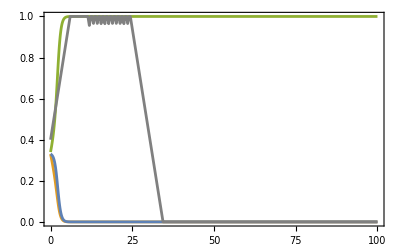

```mathematica
Plot[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t]}/.sol[{0.33,0.33},True]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]]
```

General::munfl: 9.20701×10^-297 1.59872×10^-13 is too small to represent as a normalized machine number; precision may be lost.

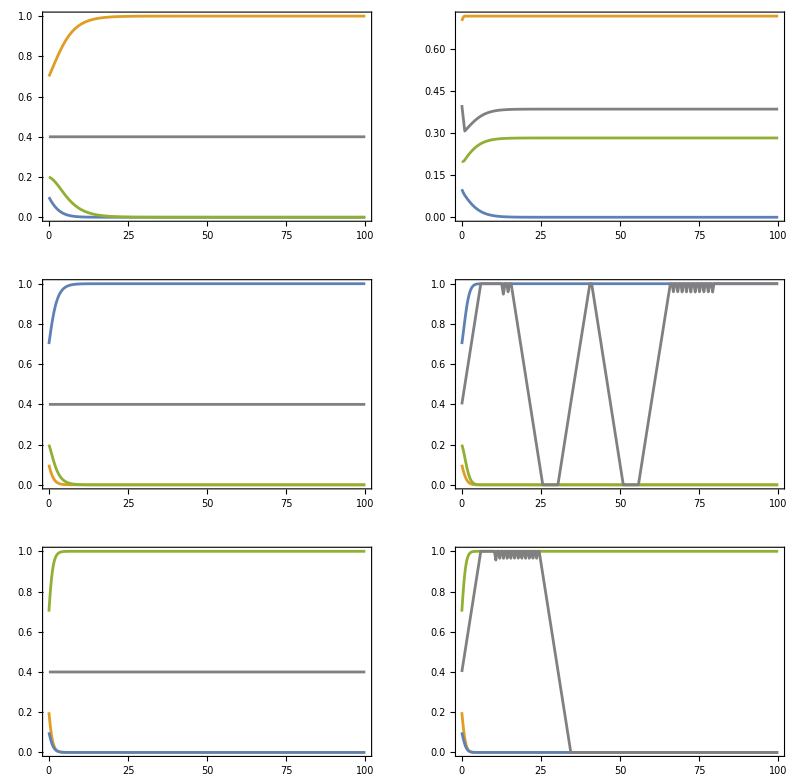

```mathematica
Table[{Plot[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t]}/.sol[sampleinits⟦i⟧,False]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]],
Plot[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t]}/.sol[sampleinits⟦i⟧,True]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]]},{i,1,3,1}]//GraphicsGrid
```